## individual gaussians fit gives nbar closer to what I measured before with rnr, 12-14uK. so don’t use the fitted offset from the RSB for the BSB and vice versa. BSB1, RSB1 = after PGC RSB2, BSB2 = after raman cooling

```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"]
kHz=10^3;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
λtrap=970 nm;
m=132.90545 amu;
```

## import data; add offset to carrier.

```mathematica
carrier0={{{-64.,0.13978494623655913},ErrorBar[{-0.03213858175998931,0.039802731840062555}]},{{-40.,0.15625},ErrorBar[{-0.03349254603917502,0.04058017490515445}]},{{-24.,0.08333333333333333},ErrorBar[{-0.024094006257488483,0.03268507154958472}]},{{-16.,0.26666666666666666},ErrorBar[{-0.043863656060683404,0.048991861188888486}]},{{-8.,0.616822429906542},ErrorBar[{-0.04787505738731046,0.04571167905570783}]},{{0.,0.8850574712643678},ErrorBar[{-0.0386565153778774,0.02990520921277806}]},{{8.,0.7403846153846154},ErrorBar[{-0.04513634392819854,0.04055758934944398}]},{{16.,0.37},ErrorBar[{-0.04677093504757068,0.04934519247331326}]},{{24.,0.11538461538461539},ErrorBar[{-0.027730027635261292,0.035056034961268606}]},{{40.,0.15306122448979592},ErrorBar[{-0.0328509003551469,0.039859764506868234}]},{{64.,0.06666666666666667},ErrorBar[{-0.02181696693578277,0.03134077645959228}]}};
carrierx=carrier0[[;;,1]][[;;,1]]-8 ;(*x offset of carrier scan vs sidebands*)
carrier=Thread[{carrierx,carrier0[[;;,1]][[;;,2]]}];
carrier=Thread[{carrier,carrier0[[;;,2]]}];

survival1={{{-103.,0.042735042735042736},ErrorBar[{-0.011390832739255924,0.015282449396830024}]},{{-98.,0.06986899563318777},ErrorBar[{-0.015042906480325767,0.018783176083515457}]},{{-93.,0.13513513513513514},ErrorBar[{-0.021315393112750505,0.024587723739341205}]},{{-88.,0.23684210526315788},ErrorBar[{-0.026968676802027164,0.029266999026803103}]},{{-83.,0.5113122171945701},ErrorBar[{-0.033600207758771705,0.03349829589215403}]},{{-78.,0.5546558704453441},ErrorBar[{-0.031780926276894106,0.0313401531281412}]},{{-73.,0.273972602739726},ErrorBar[{-0.029059132164071244,0.031113926684619264}]},{{-68.,0.23809523809523808},ErrorBar[{-0.026856746110424573,0.029114545782017387}]},{{-63.,0.12350597609561753},ErrorBar[{-0.019285882926979067,0.02227393073574402}]},{{-58.,0.09090909090909091},ErrorBar[{-0.017192841096295847,0.020719486864320916}]},{{-53.,0.0963302752293578},ErrorBar[{-0.018178985914218668,0.021865467418973383}]},{{50.,0.05286343612334802},ErrorBar[{-0.012986999061439602,0.016909249621761095}]},{{55.,0.045454545454545456},ErrorBar[{-0.01162211443459072,0.015363229286816688}]},{{60.,0.05752212389380531},ErrorBar[{-0.01362717574929638,0.017525659239218817}]},{{65.,0.08438818565400844},ErrorBar[{-0.016356216664197218,0.019848752919205556}]},{{70.,0.13852813852813853},ErrorBar[{-0.021175517149636017,0.024291653886462428}]},{{75.,0.16736401673640167},ErrorBar[{-0.022750290487743657,0.02552225701494032}]},{{80.,0.27615062761506276},ErrorBar[{-0.027942041327701145,0.029807452764242237}]},{{85.,0.33624454148471616},ErrorBar[{-0.030446851312356082,0.031870811821184675}]},{{90.,0.1762114537444934},ErrorBar[{-0.023852146335756108,0.02669239674150614}]},{{95.,0.18502202643171806},ErrorBar[{-0.02437241471414145,0.027135379394565007}]},{{100.,0.11013215859030837},ErrorBar[{-0.01909298406838586,0.02251287741408492}]},{{105.,0.06521739130434782},ErrorBar[{-0.014471917444882486,0.018236269035321037}]},{{110.,0.045081967213114756},ErrorBar[{-0.011528270056928733,0.015241886651107373}]}};
survival2={{{-103.,0.05847953216374269},ErrorBar[{-0.01550796954595974,0.020641928474288307}]},{{-98.,0.011976047904191617},ErrorBar[{-0.005976015796766543,0.011785824750288072}]},{{-93.,0.06741573033707865},ErrorBar[{-0.016479732520559433,0.021313076315675875}]},{{-88.,0.22282608695652173},ErrorBar[{-0.02913383328796318,0.03213030802356842}]},{{-83.,0.42134831460674155},ErrorBar[{-0.03646970918799003,0.037348498968920285}]},{{-78.,0.4228571428571429},ErrorBar[{-0.03680190913051784,0.03767853250714115}]},{{-73.,0.23391812865497075},ErrorBar[{-0.030767965274431958,0.033861940522629974}]},{{-68.,0.15757575757575756},ErrorBar[{-0.026290821280784804,0.030416414563004646}]},{{-63.,0.046632124352331605},ErrorBar[{-0.012980494976170126,0.01765439060140382}]},{{-58.,0.04},ErrorBar[{-0.01238679407095919,0.017614066798231916}]},{{-53.,0.023391812865497075},ErrorBar[{-0.00908212172260171,0.014624077386956397}]},{{50.,0.060240963855421686},ErrorBar[{-0.015965856335296215,0.021232431618464803}]},{{55.,0.021621621621621623},ErrorBar[{-0.008398336377056682,0.013542189908006992}]},{{60.,0.011695906432748537},ErrorBar[{-0.005836501532739878,0.011514456109103267}]},{{65.,0.016666666666666666},ErrorBar[{-0.007212823473295571,0.01255352328913351}]},{{70.,0.010869565217391304},ErrorBar[{-0.005424895135183499,0.01071279172742792}]},{{75.,0.016666666666666666},ErrorBar[{-0.007212823473295571,0.01255352328913351}]},{{80.,0.022988505747126436},ErrorBar[{-0.00892638420356883,0.014377944137887386}]},{{85.,0.01910828025477707},ErrorBar[{-0.008265279329569929,0.014352516288370216}]},{{90.,0.017142857142857144},ErrorBar[{-0.007418169867699555,0.012905182854712538}]},{{95.,0.028409090909090908},ErrorBar[{-0.01010444931529815,0.015433160152483572}]},{{100.,0.031088082901554404},ErrorBar[{-0.010275772204812728,0.015109915680054438}]},{{105.,0.023809523809523808},ErrorBar[{-0.009243389532727242,0.014878779783502105}]},{{110.,0.},ErrorBar[{0.,0.006024096385542169}]}};
```

## separate into RSB, BSB

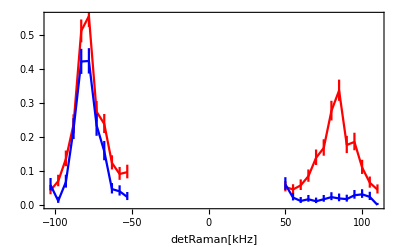

```mathematica
RSB1=Cases[survival1,x_/;x[[1,1]]<0];
BSB1=Cases[survival1,x_/;x[[1,1]]>0];
RSB2=Cases[survival2,x_/;x[[1,1]]<0];
BSB2=Cases[survival2,x_/;x[[1,1]]>0];
ErrorListPlot[{RSB1,RSB2,BSB1,BSB2},PlotStyle->{Red,Blue,Red,Blue},Joined->True,Axes->False,Frame->True,FrameLabel->{"detRaman[kHz]",""}]
```

# fit (using independent gaussians for each peak)

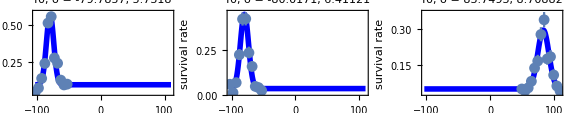

```mathematica
fits=Reap[
Do[
{dataaa1,signf}=ii;
dataaa=dataaa1[[;;,1]];
gauss=offs-A Exp[-(f-f0)^2/(2 σ^2)];
{offs0,A0,f00,σ0}={0,-.3,signf  80,10};

nlm=NonlinearModelFit[dataaa,gauss,{{offs,offs0},{ A,A0}, {f0,f00}, {σ,σ0}},f(*,Weights->weights*)];
fit=nlm["BestFitParameters"];


a=Show[{
Plot[
gauss/.fit,{f,survival1[[1,1,1]],survival1[[-1,1,1]]},PlotStyle->{Thickness[.01],Blue},Frame->{True,True},Axes->False,FrameLabel->{knobStr,"survival rate"},PlotRange->All,PlotLabel->"f0, σ = " <>ToString[f0/.fit]<>", "<>ToString[σ/.fit] 
],

ErrorListPlot[dataaa1]
}];

Sow[{fit,a}]
,{ii,{{RSB1,-1},{RSB2,-1},{BSB1,1}}}]
][[2,1]];
GraphicsGrid[{fits[[;;,2]]}]
{fitRSB1,fitRSB2,fitBSB1}=fits[[;;,1]];
```

## fit carrier

```mathematica
tPulse=35 10^-3;(*if kHz-->1, then us-->1e-3*)
RabiLine=offs+(A (fR)^2)/((f-f0)^2+(fR)^2)Sin[2π (√((f-f0)^2+fR^2))/2 tPulse]^2;
{offs0,A0,f00,fR0}={0,.8,0,20};

nlm=NonlinearModelFit[carrier[[;;,1]],RabiLine,{{offs,offs0},{ A,A0}, {f0,f00}, {fR,fR0}},f(*,Weights->weights*)];
fitcarrier=nlm["BestFitParameters"];
```

## plot with fits

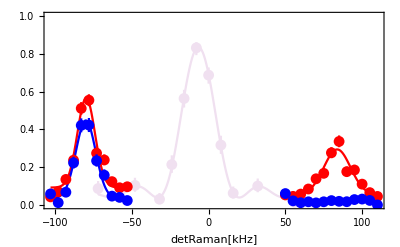

```mathematica
(*remove bkgrd*)
offsCarrier=offs/.fitBSB1;offs/.fitcarrier;
carrierSub=Thread[{
Thread[
{
carrier[[;;,1]][[;;,1]],
carrier[[;;,1]][[;;,2]]-offsCarrier
}
],
carrier[[;;,2]]
}];

Show[{
(*plot carrier+fit*)
Plot[{RabiLine-offsCarrier/.fitcarrier},{f,carrier[[1,1,1]],carrier[[-1,1,1]]},PlotRange->{All,{0,1}},PlotStyle->LightPurple,Axes->False,Frame->True,FrameLabel->{"detRaman[kHz]",""}],
ErrorListPlot[carrierSub,PlotStyle->LightPurple],

Plot[{gauss/.fitRSB1,gauss/.fitRSB2},{f,RSB1[[1,1,1]],RSB1[[-1,1,1]]},PlotRange->{All,{0,1}},PlotStyle->{Red,Blue},Axes->False,Frame->True,FrameLabel->{"detRaman[kHz]",""}],
Plot[{gauss/.fitBSB1},{f,BSB1[[1,1,1]],BSB1[[-1,1,1]]},PlotRange->{All,{0,1}},PlotStyle->Red],
ErrorListPlot[{RSB1,RSB2,BSB1,BSB2},PlotStyle->{Red,Blue,Red,Blue}]
}]
```

## calculate nbar

```mathematica
Clear[nbar,nbar1,nbar2,fitsurv1]
ftrap=((f0/.fitBSB1)-(f0/.fitRSB1))/2 kHz;
(*use fitted offset from RSB*)
offset2=offs/.fitRSB2;
(*use measured offset from BSB wings*)
offset2=Mean[BSB2[[{1,2,-1}]][[;;,1]][[;;,2]]];

BSB2mod=Cases[BSB2,x_/;x[[1,1]]>0];

ARSB2=Re[Integrate[gauss-offs/.fitRSB2,{f,-Infinity,Infinity}]];
ABSB2=Mean[Differences[BSB2mod[[;;,1]][[;;,1]]]] Total[(BSB2mod[[;;,1]][[;;,2]]-offset2) Boole[Positive[#]&/@(BSB2mod[[;;,1]][[;;,2]]-offset2)]];

nbar1=1/((σ A/.fitRSB1)/(σ A/.fitBSB1)-1);
nbar2=1/(ARSB2/ABSB2-1);

(*get temp*)
T1=T/uK/.Solve[nbar1==1/(Exp[(ℏ 2π f)/(kB T)]-1)/.f->(ftrap),T][[1]];
T2=T/uK/.Solve[nbar2==1/(Exp[(ℏ 2π f)/(kB T)]-1)/.f->(ftrap),T][[1]];
(*get %ground state occupation*)
P01=nbar^n/(nbar+1)^(n+1)/.n->0/.nbar->nbar1;
P02=nbar^n/(nbar+1)^(n+1)/.n->0/.nbar->nbar2;

{
{"nbar1","nbar2","T1[uK]","T2[uK]","P01","P02"}
,
Round[{nbar1,nbar2,T1,T2, P01,P02},.01]
}//TableForm
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

nbar1 | nbar2 | T1[uK] | T2[uK] | P01 | P02
3.41 | 0.03 | 15.25 | 1.1 | 0.23 | 0.97

# fit (using double gaussians for the pgc case)

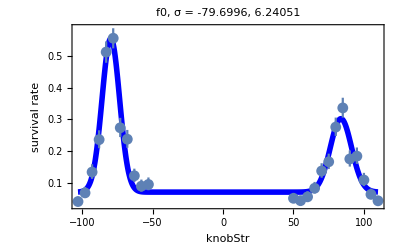

0.0723069+0.23007 ⅇ^(-0.00872473 (-83.6831+f)^2)+0.481086 ⅇ^(-0.0128389 (79.6996+f)^2)

```mathematica
Clear[σ2, fitsurv1]
dataaa1=survival1;
dataaa=dataaa1[[;;,1]];

gauss2=offs-A Exp[-(f-f0)^2/(2 σ^2)]-A2 Exp[-(f-f02)^2/(2 σ2^2)];
{offs0,A0,f00,σ0,A02,f020,σ20}={0,-.3,-80,10,-.3,80,10};

nlm=NonlinearModelFit[dataaa,gauss2,{{offs,offs0},{ A,A0}, {f0,f00}, {σ,σ0},{ A2,A02}, {f02,f020}, {σ2,σ20}},f(*,Weights->weights*)];
fit=nlm["BestFitParameters"];

Show[{
Plot[
gauss2/.fit,{f,survival1[[1,1,1]],survival1[[-1,1,1]]},PlotStyle->{Thickness[.01],Blue},Frame->{True,True},Axes->False,FrameLabel->{knobStr,"survival rate"},PlotRange->All,PlotLabel->"f0, σ = " <>ToString[f0/.fit]<>", "<>ToString[σ/.fit] 
],

ErrorListPlot[dataaa1]
}]
Print[gauss2/.fit]

fitsurv1=fit;
```

## plot with fits

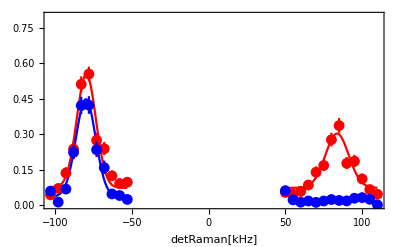

```mathematica
Show[{
Plot[{gauss2/.fitsurv1,gauss/.fitRSB2},{f,RSB2[[1,1,1]],RSB2[[-1,1,1]]},PlotRange->{All,{0,.8}},PlotStyle->{Red,Blue},Axes->False,Frame->True,FrameLabel->{"detRaman[kHz]",""}],
Plot[{gauss2/.fitsurv1},{f,BSB2[[1,1,1]],BSB2[[-1,1,1]]},PlotRange->{All,{0,.8}},PlotStyle->Red],
ErrorListPlot[{RSB1,RSB2,BSB1,BSB2},PlotStyle->{Red,Blue,Red,Blue}]
}]
```

## calculate nbar

```mathematica
Clear[nbar,T1,ftrap]
ftrap=((f02-f0)/2 kHz/.fitsurv1);

nbar1=1/((σ A/.fitsurv1)/(σ2 A2/.fitsurv1)-1);
nbar2=1/(ARSB2/ABSB2-1);

(*get temp*)
T1=T/uK/.Solve[nbar1==1/(Exp[(ℏ 2π f)/(kB T)]-1)/.f->ftrap,T][[1]];
(*get %ground state occupation*)
P01=nbar^n/(nbar+1)^(n+1)/.n->0/.nbar->nbar1;


{
{"nbar1","nbar2","T1[uK]","T2[uK]","P01","P02"}
,
Round[{nbar1,nbar2,T1,T2, P01,P02},.01]
}//TableForm
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

nbar1 | nbar2 | T1[uK] | T2[uK] | P01 | P02
1.38 | 0.03 | 7.2 | 1.1 | 0.42 | 0.97

## include errors, plot carrier alongside, estimate bkgrd for BSB2

```mathematica
Clear[σ0]
nbar=1/((σ A)/(σ2 A2)-1);
Δnbar=√((D[nbar, σ])^2(#[[4]])^2+(D[nbar, A])^2(#[[2]])^2+(D[nbar, σ2])^2(#[[7]])^2+(D[nbar, A2])^2(#[[5]])^2)&@nlm["ParameterErrors"]/.fit
Print["nbar="<>ToString[nbar/.fit]<>"+/-"<>ToString[Δnbar]];
```

0.801519

nbar=1.3817+/-0.801519

```mathematica
fit
```

{offs→0.0723069,A→-0.481086,f0→-79.6996,σ→6.24051,A2→-0.23007,f02→83.6831,σ2→7.57023}

```mathematica
(*nbar of radial dir. and error if you have rnr*)
If[fitRNR,
dftrap=1 kHz;
nbar=1/(Exp[(ℏ 2π f)/(kB T)]-1);
Δnbar=√((D[nbar, T])^2(chisquareErr uK)^2+(D[nbar, f])^2(dftrap)^2)/.T->TBestFit uK/.f->frad;
```

```mathematica
fitsurv1
```

{offs→0.0723069,A→-0.481086,f0→-79.6996,σ→6.24051,A2→-0.23007,f02→83.6831,σ2→7.57023}

```mathematica
fitBSB1
fitRSB1
```

{offs→0.0529923,A→-0.240892,f0→83.7493,σ→8.70882}

{offs→0.0920974,A→-0.473393,f0→-79.7857,σ→5.7318}